EJERCICIO 1. Sea X una variable aleatoria con función de distribución dada por 
F(x)=Piecewise[{{0, x<0}, {x^2/16, 0≤x<2}, {1/4, 2≤x<4}, {(2x-5)/8, 4≤x<5}, {1-5/(4x), x≥5}}]
  Descomponer La función de distribución F como mixtura de funciones de distribución.
Calcular  Px[(1,4]], Px[[2,5)], Px[(0,4]|[2,5)](condicionada)

Estudiar con detalle la función  de distribución F. 
(Es decir, dar la función de densidad en el caso de ser absolutamente continua, los puntos de discontinuidad y sus probabilidades y la  pseudodensidad en el caso de ser mixta o los puntos de discontinuidad y sus probabilidades en el caso de ser discreta)

```mathematica
(*Px[(1,4]]*)
```

```mathematica
F[4] - F[1]
```

5/16

```mathematica
(*Px[[2,5)]*)
```

```mathematica
Limit[F[t], t->5, Direction->1] - Limit[F[t],t->2, Direction->2]
```

3/8

```mathematica
(*Px[(0,3]/[2,5)]= P((0,3) int [2, 5))/P([2, 5))=P( *)
(F[4]-Limit[F[t], t->2, Direction->1])/(Limit[F[t], t->5, Direction->1]-Limit[F[t], t->2, Direction -> 1])
```

1/3

```mathematica
Definición y representación  la función de distribución.
```

```mathematica
F[x_]:= Piecewise[{{0,x<0},{x^2/16,0⩽x<2},{1/4,2⩽x<4},{(2x-5)/8,4⩽x<5},{1-5/(4x), x⩾5}}]
```

```mathematica
F[x]
```

Piecewise[{{0, x<0}, {x^2/16, 0≤x<2}, {1/4, 2≤x<4}, {1/8 (-5+2 x), 4≤x<5}, {1-5/(4 x), x≥5}, {0, True}}]

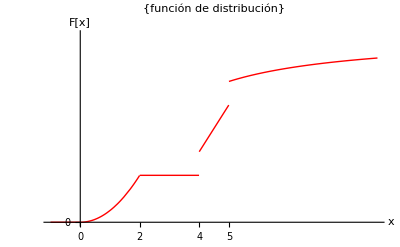

```mathematica
Plot[ F[x] ,{x,-1, 10}, PlotRange->{{-1,10},{0,1}}, AxesLabel->{"x","F[x]"}, PlotStyle->{Red,Thick}, PlotLabel->{"función de distribución"}, Ticks->{{0,2,4,5}}]
```

```mathematica
Volvemos a representar la función F[x] indicanto algunas marcas en el eje Y
```

```mathematica
F[2]
```

1/4

```mathematica
F[4]
```

3/8

```mathematica
F[4]//N
```

0.375

```mathematica
Limit[F[t],t->4, Direction->1]//N
```

0.25

```mathematica
F[5]//N
```

0.75

```mathematica
Limit[F[t],t->5, Direction->1]//N
```

0.625

Voy a definir la asíntota en y = 1

```mathematica
A[x_]:=1 (*asíntota en y=1*)
```

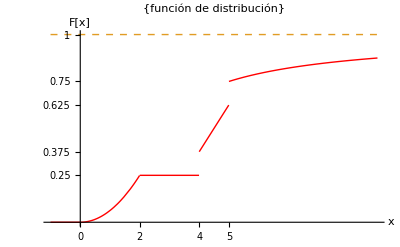

```mathematica
Plot[{F[x],A[x]}, {x,-1,10},PlotRange->{{-1,10},{0,1}},AxesLabel->{"x","F[x]"},PlotStyle->{{Red,Thick},{Dashed,Thick}},PlotLabel->{"función de distribución"},Ticks->{{0, 2,4,5},{0.25,0.375,0.625,0.75,1}}]
```

```mathematica
Cálculo  la probabilidad en los puntos de discontinuidad
```

```mathematica
P[x_]:=F[x]-Limit[F[t], t->x, Direction->1]
```

```mathematica
F[4]
```

3/8

```mathematica
Limit[F[t], t->4, Direction->1]
```

1/4

```mathematica
P[4]
```

1/8

```mathematica
F[5]
```

3/4

```mathematica
Limit[F[t], t->5, Direction->1]
```

5/8

```mathematica
P[5]
```

1/8

```mathematica
P[4]+P[5]
```

1/4

```mathematica
Descomposición de F como mixtura de funciones de distribución
```

```mathematica
Fd[x_]:=Piecewise[{{0,x<4},{1/8,4≤x<5},{2/8,x≥5}}]
```

```mathematica
Fd[x]
```

Piecewise[{{0, x<4}, {1/8, 4≤x<5}, {1/4, x≥5}, {0, True}}]

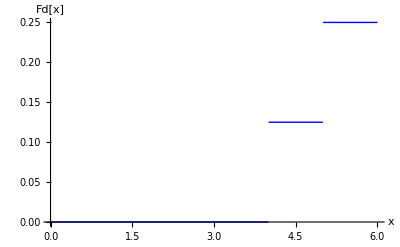

```mathematica
Plot[Fd[x],{x,0,6}, AxesLabel->{"x","Fd[x]"},PlotStyle->{{Blue,Thick}} ]
```

```mathematica
Fc[x_]:=F[x]-Fd[x]
```

```mathematica
Fc[x]
```

-(Piecewise[{{0, x<4}, {1/8, 4≤x<5}, {1/4, x≥5}, {0, True}}])+(Piecewise[{{0, x<0}, {x^2/16, 0≤x<2}, {1/4, 2≤x<4}, {1/8 (-5+2 x), 4≤x<5}, {1-5/(4 x), x≥5}, {0, True}}])

```mathematica
Simplify[Fc[x]]
```

Piecewise[{{1/4, 2≤x<4}, {1/4 (-3+x), 4≤x<5}, {x^2/16, 0≤x<2}, {3/4-5/(4 x), x≥5}, {0, True}}]

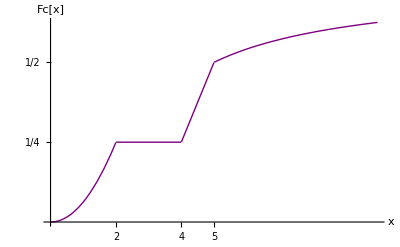

```mathematica
Plot[Fc[x],{x,0,10} ,AxesLabel->{"x","Fc[x]"},PlotStyle->{{Purple,Thick}}, Ticks->  {{2,4,5},{1/4, 1/2}}]
```

```mathematica
Limit[Fd[x],x->∞]
```

1/4

```mathematica
F1[x_]:=Fd[x]/0.25
```

```mathematica
F1[x]
```

4. (Piecewise[{{0, x<4}, {1/8, 4≤x<5}, {1/4, x≥5}, {0, True}}])

```mathematica
Simplify[F1[x]]
```

Piecewise[{{0., x<4}, {0.5, 4≤x<5}, {1., True}}]

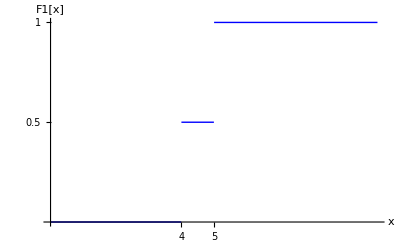

```mathematica
Plot[F1[x],{x,0,10}, AxesLabel->{"x","F1[x]"},PlotStyle->{{Blue,Thick}}, Ticks->{{4,5},{0.5,1}} ]
```

```mathematica
F2[x_]:=Fc[x]/0.75
```

```mathematica
F2[x]
```

1.33333 (-(Piecewise[{{0, x<4}, {1/8, 4≤x<5}, {1/4, x≥5}, {0, True}}])+(Piecewise[{{0, x<0}, {x^2/16, 0≤x<2}, {1/4, 2≤x<4}, {1/8 (-5+2 x), 4≤x<5}, {1-5/(4 x), x≥5}, {0, True}}]))

```mathematica
Simplify[F2[x]]
```

Piecewise[{{0., x<0}, {0.333333, 2≤x<4}, {0.0833333 x^2, 0≤x<2}, {-1.+0.333333 x, 4≤x<5}, {1.-1.66667/x, True}}]

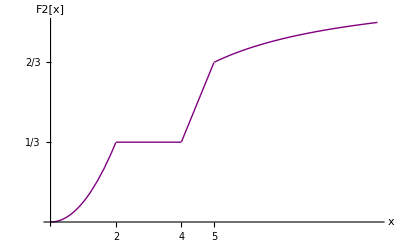

```mathematica
Plot[F2[x],{x,0,10}, PlotRange->All, AxesLabel->{"x","F2[x]"},PlotStyle->{{Purple,Thick}}, Ticks->  {{2,4,5},{1/3, 2/3}}]
```

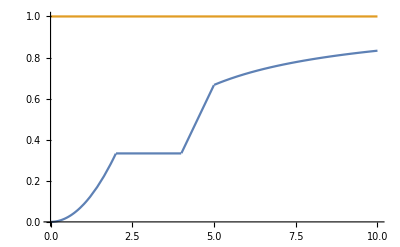

```mathematica
Plot[{F2[x],A[x]},{x,0,10}]
```

```mathematica
Cálculo de probabilidades
```

```mathematica
P[4]
```

1/8

```mathematica
P[5]
```

1/8

```mathematica
P[4]+P[5]
```

1/4

```mathematica
Calculamos y representamos  la pseudodensidad
```

```mathematica
D[F[x],x]
```

Piecewise[{{0, x<0||x==0}, {x/8, 0<x<2}, {0, 2<x<4}, {1/4, 4<x<5}, {1/x-(-5+4 x)/(4 x^2), x>5}, {Indeterminate, True}}]

```mathematica
Simplify[%] (*% sirve para simplifica el resultado anterior*)
```

Piecewise[{{1/4, 4<x<5}, {5/(4 x^2), x>5}, {x/8, 0<x<2}, {0, x≤0||2<x<4}, {Indeterminate, True}}]

```mathematica
f(x)=Piecewise[{{x/8, 0<x<2}, {1/4, 4<x<5}, {5/(4 x^2), x>5}}]
```

```mathematica
f[x_]:=Piecewise[{{x/8, 0<x<2},{0,2<x<4},{1/4, 4<x<5},{5/(4x^2),x>5}}]
```

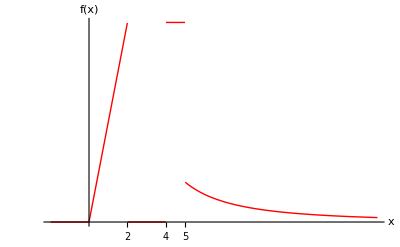

```mathematica
Plot[f[x],{x,-2,15},PlotStyle->{Red, Thick}, AxesLabel->{"x","f(x)"},Ticks->{{2,4,5}},PlotRange->All]
```

```mathematica
Limit[f[t], t->2,Direction->1]
```

1/4

```mathematica
Limit[f[t],t->5, Direction->-1]//N
```

0.05

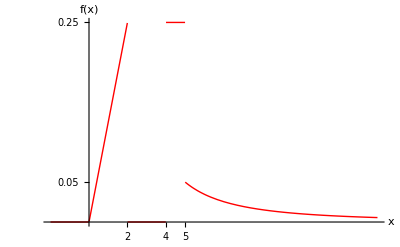

```mathematica
Plot[f[x],{x,-2,15},PlotStyle->{Red, Thick}, AxesLabel->{"x","f(x)"},Ticks->{{2,4,5},{0.05,0.25}},PlotRange->All]
```

```mathematica
Integrate[x/8, {x,0, 2}]
```

1/4

```mathematica
Integrate[1/4, {x,4, 5}]
```

1/4

```mathematica
Integrate[5/(4x^2), {x,5,  ∞}]
```

1/4

```mathematica
Integrate[f[x], {x,0, ∞}]
```

3/4

```mathematica
P[4]+P[5]+Integrate[f[x], {x,0, ∞}]
```

1

Por tanto P(DX)+∫_0^∞ f^*[x]ⅆx =1